```mathematica
notes=MapThread[{#1,#2}&,{Range[12],{"C","C#","D","D#","E","F","F#","G","G#","A","A#","B"}}];
freqs1={16.351,17.324,18.354,19.445,20.601,21.827,23.124,24.499,25.956,27.5,29.135,30.868};
wavelengths1={20.812,19.643,18.54,17.5,16.518,15.59,14.716,13.89,13.11,12.374,11.68,11.024};
freqs9={8372.018,8869.844,9397.272,9956.064,10548.084,11175.304,11839.82,12543.856,13289.752,14080,14917.24,15804.264};
wavelengths9={0.041,0.038,0.036,0.034,0.032,0.03,0.029,0.027,0.026,0.024,0.023,0.022};
freqPlot1=ListPlot[freqs1, Ticks->{notes,Automatic},PlotStyle->Directive[Orange,Specularity[White,40]],PlotMarkers->{Automatic,Medium},AxesLabel->{"音符","频率(Hz)"},
PlotLabel->"第一音阶"];
wavePlot1=ListPlot[wavelengths1,Ticks->{notes,Automatic},PlotStyle->Directive[Orange,Specularity[White,40]],PlotMarkers->{Automatic,Medium},
AxesLabel->{"音符","波长(m)"},
PlotLabel->"第一音阶"];
freqPlot9=ListPlot[freqs9,Ticks->{notes,Automatic},PlotStyle->Directive[Green,Specularity[White,40]],PlotMarkers->{Automatic,Medium},AxesLabel->{"音符","频率(Hz)"},
PlotLabel->"第九音阶"];
wavePlot9=ListPlot[wavelengths9,Ticks->{notes,Automatic},PlotStyle->Directive[Green,Specularity[White,40]],PlotMarkers->{Automatic,Medium},AxesLabel->{"音符","波长(m)"},
PlotLabel->"第九音阶"];
```

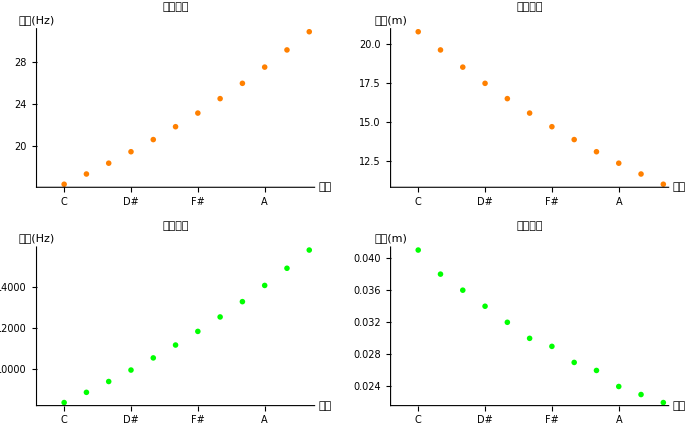

```mathematica
GraphicsGrid[{{freqPlot1,wavePlot1},{freqPlot9,wavePlot9}}]
```

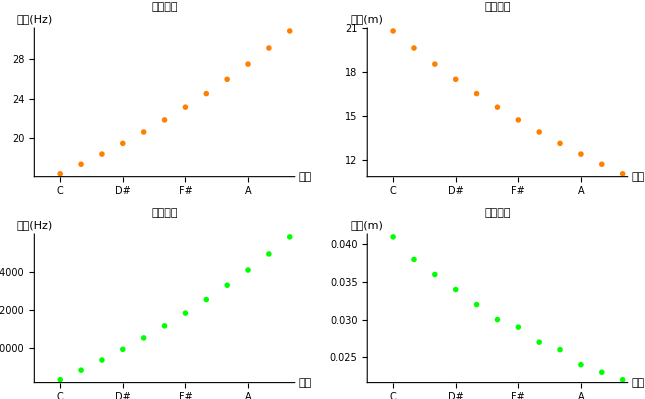

```mathematica
Show[%262,ImageSize->{645,399},AspectRatio->Full]
```

```mathematica
Export["/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_1_and_9.svg",%264,"SVG"]
```

/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_1_and_9.svg

```mathematica
Export["/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_1_and_9.png",%264,"PNG"]
```

/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_1_and_9.png

```mathematica
Export["/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_1_and_9.png",%262,"PNG"]
```

/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_1_and_9.png

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["music.csv"];
```

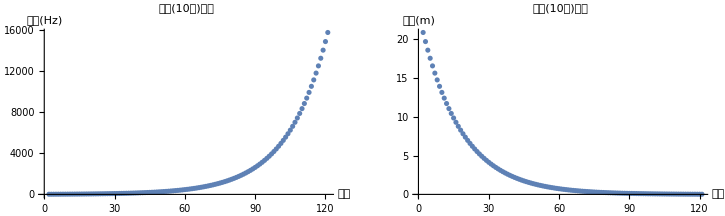

```mathematica
freqPlotAll=ListPlot[data[[All,3]],AxesLabel->{"音符","频率(Hz)"},
PlotLabel->"所有(10个)音阶"];
wavePlotAll=ListPlot[data[[All,4]],AxesLabel->{"音符","波长(m)"},
PlotLabel->"所有(10个)音阶"];
GraphicsGrid[{{freqPlotAll,wavePlotAll}}]
```

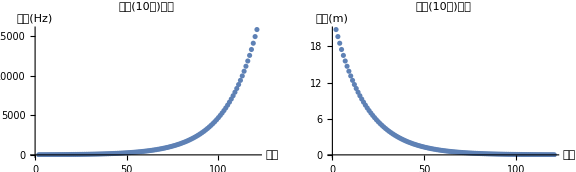

```mathematica
Show[%279,ImageSize->Large]
```

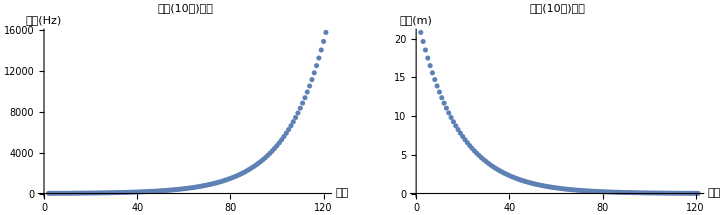

```mathematica
Show[%281,ImageSize->721,AspectRatio->Automatic]
```

```mathematica
Export["/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_all.svg",%282,"SVG"]
```

/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_all.svg

```mathematica
Export["/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_all.eps",%282,"EPS"]
```

/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_all.eps

```mathematica
Export["/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_all.png",%282,"PNG"]
```

/Users/xiaotingtang/Documents/Blog/source/_drafts/游泳奇想/freq_wavelength_all.png

```mathematica
freq[n_]:=440 (2^(1/12))^n
```

```mathematica
freq[2+5*12]
```

14080 2^(1/6)

```mathematica
N[14080 2^(1/6)]
```

15804.3

```mathematica
ScientificForm[15804.265640195972]
```

1.58043×10^4

```mathematica
NumberForm[15804.265640195972,16]
```

15804.26564019597

```mathematica
N[28160 2^(1/6)]
```

31608.5

```mathematica
N[440 2^(1/4)]
```

523.251

```mathematica
N[55/216]
```

0.25463

```mathematica
Table[N[freq[i+5*12],10],{i,3,15}]
```

{16744.03618,17739.68838,18794.54515,19912.12696,21096.16364,22350.60681,23679.64305,25087.7079,26579.50065,28160.,29834.48074,31608.53128,33488.07236}